```mathematica
SetDirectory@NotebookDirectory[]
```

/Users/leima/Dropbox/Research/git/15summer/code

```mathematica
sne=Import["data/neordered.txt","Table"];
```

```mathematica
sne[[1]]
```

{0.00819005,2.00852}

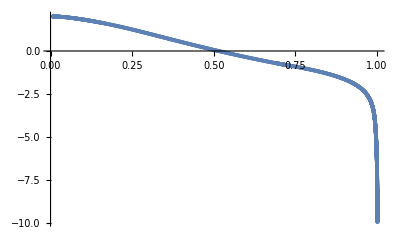

```mathematica
sneplt=Table[sne[[i]],{i,200,Length@sne-1800}];
snepl=ListPlot[sne,PlotRange->Full,ImageSize->Full]
```

```mathematica
fitted=LinearModelFit[sneplt,x,x]
```

FittedModel[2.2901-4.33005 x]

```mathematica
fittedPlt=Plot[Normal@fitted,{x,0,1}];
```

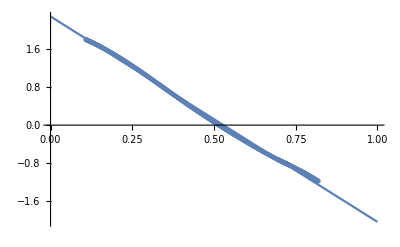

```mathematica
Show[fittedPlt,snepl,ImageSize->Full]
```

```mathematica
solMSW=Solve[2c s ==Sin[2 Subscript[θ, v]]/Sqrt[(Δ̂)^2+1-2 Δ̂ Cos[2 Subscript[θ, v]]]&&c^2-s^2== (Cos[2 Subscript[θ, v]]-Δ̂)/Sqrt[(Δ̂)^2+1-2 Δ̂ Cos[2 Subscript[θ, v]]],{c,s}]//FullSimplify
```

{{c→(√(-(-Cos[2 θ_v]+Δ̂+√(1-2 Cos[2 θ_v] Δ̂+(Δ̂)^2))/(√(1-2 Cos[2 θ_v] Δ̂+(Δ̂)^2))))/(√2),s→-(Csc[2 θ_v] (Cos[2 θ_v]-Δ̂+√(1-2 Cos[2 θ_v] Δ̂+(Δ̂)^2)) √(-(-Cos[2 θ_v]+Δ̂+√(1-2 Cos[2 θ_v] Δ̂+(Δ̂)^2))/(√(1-2 Cos[2 θ_v] Δ̂+(Δ̂)^2))))/(√2)},{c→-(√(-(-Cos[2 θ_v]+Δ̂+√(1-2 Cos[2 θ_v] Δ̂+(Δ̂)^2))/(√(1-2 Cos[2 θ_v] Δ̂+(Δ̂)^2))))/(√2),s→(Csc[2 θ_v] (Cos[2 θ_v]-Δ̂+√(1-2 Cos[2 θ_v] Δ̂+(Δ̂)^2)) √(-(-Cos[2 θ_v]+Δ̂+√(1-2 Cos[2 θ_v] Δ̂+(Δ̂)^2))/(√(1-2 Cos[2 θ_v] Δ̂+(Δ̂)^2))))/(√2)},{c→-(√((Cos[2 θ_v]-Δ̂+√(1-2 Cos[2 θ_v] Δ̂+(Δ̂)^2))/(√(1-2 Cos[2 θ_v] Δ̂+(Δ̂)^2))))/(√2),s→-(Csc[2 θ_v] √((Cos[2 θ_v]-Δ̂+√(1-2 Cos[2 θ_v] Δ̂+(Δ̂)^2))/(√(1-2 Cos[2 θ_v] Δ̂+(Δ̂)^2))) (-Cos[2 θ_v]+Δ̂+√(1-2 Cos[2 θ_v] Δ̂+(Δ̂)^2)))/(√2)},{c→(√((Cos[2 θ_v]-Δ̂+√(1-2 Cos[2 θ_v] Δ̂+(Δ̂)^2))/(√(1-2 Cos[2 θ_v] Δ̂+(Δ̂)^2))))/(√2),s→(Csc[2 θ_v] √((Cos[2 θ_v]-Δ̂+√(1-2 Cos[2 θ_v] Δ̂+(Δ̂)^2))/(√(1-2 Cos[2 θ_v] Δ̂+(Δ̂)^2))) (-Cos[2 θ_v]+Δ̂+√(1-2 Cos[2 θ_v] Δ̂+(Δ̂)^2)))/(√2)}}

```mathematica
c/.solMSW[[1]]
s/.solMSW[[1]]
```

(√(-(-Cos[2 θ_v]+Δ̂+√(1-2 Cos[2 θ_v] Δ̂+(Δ̂)^2))/(√(1-2 Cos[2 θ_v] Δ̂+(Δ̂)^2))))/(√2)

-(Csc[2 θ_v] (Cos[2 θ_v]-Δ̂+√(1-2 Cos[2 θ_v] Δ̂+(Δ̂)^2)) √(-(-Cos[2 θ_v]+Δ̂+√(1-2 Cos[2 θ_v] Δ̂+(Δ̂)^2))/(√(1-2 Cos[2 θ_v] Δ̂+(Δ̂)^2))))/(√2)

```mathematica
Series[D[c/.solMSW[[1]],Δ̂],{Δ̂,0,0}]//FullSimplify
Series[D[c/.solMSW[[1]],Δ̂],{Δ̂,0,1}]//FullSimplify
Series[D[s/.solMSW[[1]],Δ̂],{Δ̂,0,1}]//FullSimplify
```

Cos[θ_v]^2 √(-Sin[θ_v]^2)+O[Δ̂]^1

Cos[θ_v]^2 √(-Sin[θ_v]^2)+1/2 Cos[θ_v]^2 (-1+5 Cos[2 θ_v]) √(-Sin[θ_v]^2) Δ̂+O[Δ̂]^2

-Cot[θ_v] (-Sin[θ_v]^2)^(3/2)-1/2 ((1+5 Cos[2 θ_v]) Cot[θ_v] (-Sin[θ_v]^2)^(3/2)) Δ̂+O[Δ̂]^2

```mathematica
Series[Sin[2 Subscript[θ, v]]/Sqrt[(Δ̂)^2+1-2 Δ̂ Cos[2 Subscript[θ, v]]],{Δ̂,0,1}]
%//Simplify
Series[(Cos[2 Subscript[θ, v]]-Δ̂)/Sqrt[(Δ̂)^2+1-2 Δ̂ Cos[2 Subscript[θ, v]]],{Δ̂,0,1}]
%//FullSimplify
```

Sin[2 θ_v]+Cos[2 θ_v] Sin[2 θ_v] Δ̂+O[Δ̂]^2

Sin[2 θ_v]+1/2 Sin[4 θ_v] Δ̂+O[Δ̂]^2

Cos[2 θ_v]+(-1+Cos[2 θ_v]^2) Δ̂+O[Δ̂]^2

Cos[2 θ_v]-Sin[2 θ_v]^2 Δ̂+O[Δ̂]^2

```mathematica
Cos[2 Subscript[θ, v]]-Sin[2 Subscript[θ, v]]^2 Δ̂
```

```mathematica
solLZ=Solve[2c s ==Sin[2 Subscript[θ, v]]+1/2 Sin[4 Subscript[θ, v]] Δ̂&&c^2-s^2== Cos[2 Subscript[θ, v]]-Sin[2 Subscript[θ, v]]^2 Δ̂,{c,s}]//FullSimplify
```

{{c→-1/2 √(2 Cos[2 θ_v]+(-1+Cos[4 θ_v]) Δ̂-2 √(1+(Δ̂)^2 Sin[2 θ_v]^2)),s→(Csc[2 θ_v] √(2 Cos[2 θ_v]+(-1+Cos[4 θ_v]) Δ̂-2 √(1+(Δ̂)^2 Sin[2 θ_v]^2)) ((-1+Cos[4 θ_v]) Δ̂+2 (Cos[2 θ_v]+√(1+(Δ̂)^2 Sin[2 θ_v]^2))))/(4+4 Cos[2 θ_v] Δ̂)},{c→1/2 √(2 Cos[2 θ_v]+(-1+Cos[4 θ_v]) Δ̂-2 √(1+(Δ̂)^2 Sin[2 θ_v]^2)),s→-(Csc[2 θ_v] √(2 Cos[2 θ_v]+(-1+Cos[4 θ_v]) Δ̂-2 √(1+(Δ̂)^2 Sin[2 θ_v]^2)) ((-1+Cos[4 θ_v]) Δ̂+2 (Cos[2 θ_v]+√(1+(Δ̂)^2 Sin[2 θ_v]^2))))/(4+4 Cos[2 θ_v] Δ̂)},{c→-1/2 √((-1+Cos[4 θ_v]) Δ̂+2 (Cos[2 θ_v]+√(1+(Δ̂)^2 Sin[2 θ_v]^2))),s→((Cot[2 θ_v]-Δ̂ Sin[2 θ_v]-Csc[2 θ_v] √(1+(Δ̂)^2 Sin[2 θ_v]^2)) √((-1+Cos[4 θ_v]) Δ̂+2 (Cos[2 θ_v]+√(1+(Δ̂)^2 Sin[2 θ_v]^2))))/(2+2 Cos[2 θ_v] Δ̂)},{c→1/2 √((-1+Cos[4 θ_v]) Δ̂+2 (Cos[2 θ_v]+√(1+(Δ̂)^2 Sin[2 θ_v]^2))),s→((-Cot[2 θ_v]+Δ̂ Sin[2 θ_v]+Csc[2 θ_v] √(1+(Δ̂)^2 Sin[2 θ_v]^2)) √((-1+Cos[4 θ_v]) Δ̂+2 (Cos[2 θ_v]+√(1+(Δ̂)^2 Sin[2 θ_v]^2))))/(2+2 Cos[2 θ_v] Δ̂)}}

```mathematica
Series[s/.solLZ,{Δ̂,0,1}]//FullSimplify
Series[c/.solLZ,{Δ̂,0,1}]//FullSimplify
```

{Cot[θ_v] √(-Sin[θ_v]^2)+Cot[θ_v] (-Sin[θ_v]^2)^(3/2) Δ̂+O[Δ̂]^2,-Cot[θ_v] √(-Sin[θ_v]^2)-Cot[θ_v] (-Sin[θ_v]^2)^(3/2) Δ̂+O[Δ̂]^2,-√(Cos[θ_v]^2) Tan[θ_v]-Cos[θ_v] √(Cos[θ_v]^2) Sin[θ_v] Δ̂+O[Δ̂]^2,√(Cos[θ_v]^2) Tan[θ_v]+Cos[θ_v] √(Cos[θ_v]^2) Sin[θ_v] Δ̂+O[Δ̂]^2}

{-√(-Sin[θ_v]^2)+Cot[θ_v]^2 (-Sin[θ_v]^2)^(3/2) Δ̂+O[Δ̂]^2,√(-Sin[θ_v]^2)+((-1+Cos[4 θ_v]) Δ̂)/(8 √(-Sin[θ_v]^2))+O[Δ̂]^2,-√(Cos[θ_v]^2)+√(Cos[θ_v]^2) Sin[θ_v]^2 Δ̂+O[Δ̂]^2,√(Cos[θ_v]^2)+((-1+Cos[4 θ_v]) Δ̂)/(8 √(Cos[θ_v]^2))+O[Δ̂]^2}

```mathematica
{{Cos[Subscript[θ, v]]-Cos[Subscript[θ, v]]Sin[Subscript[θ, v]]^2 Δ̂,-Sin[Subscript[θ, v]]-Cos[Subscript[θ, v]]^2Sin[Subscript[θ, v]] Δ̂},{Sin[Subscript[θ, v]]+Cos[Subscript[θ, v]]^2Sin[Subscript[θ, v]] Δ̂,Cos[Subscript[θ, v]]-Cos[Subscript[θ, v]]Sin[Subscript[θ, v]]^2 Δ̂}}.{{-Sin[Subscript[θ, v]],Cos[Subscript[θ, v]]},{-Cos[Subscript[θ, v]],-Sin[Subscript[θ, v]]}}
%//MatrixForm//FullSimplify
```

{{-Cos[θ_v] (-Sin[θ_v]-Cos[θ_v]^2 Δ̂ Sin[θ_v])-Sin[θ_v] (Cos[θ_v]-Cos[θ_v] Δ̂ Sin[θ_v]^2),-Sin[θ_v] (-Sin[θ_v]-Cos[θ_v]^2 Δ̂ Sin[θ_v])+Cos[θ_v] (Cos[θ_v]-Cos[θ_v] Δ̂ Sin[θ_v]^2)},{-Sin[θ_v] (Sin[θ_v]+Cos[θ_v]^2 Δ̂ Sin[θ_v])-Cos[θ_v] (Cos[θ_v]-Cos[θ_v] Δ̂ Sin[θ_v]^2),Cos[θ_v] (Sin[θ_v]+Cos[θ_v]^2 Δ̂ Sin[θ_v])-Sin[θ_v] (Cos[θ_v]-Cos[θ_v] Δ̂ Sin[θ_v]^2)}}

(Cos[θ_v] Δ̂ Sin[θ_v] | 1
-1 | Cos[θ_v] Δ̂ Sin[θ_v])

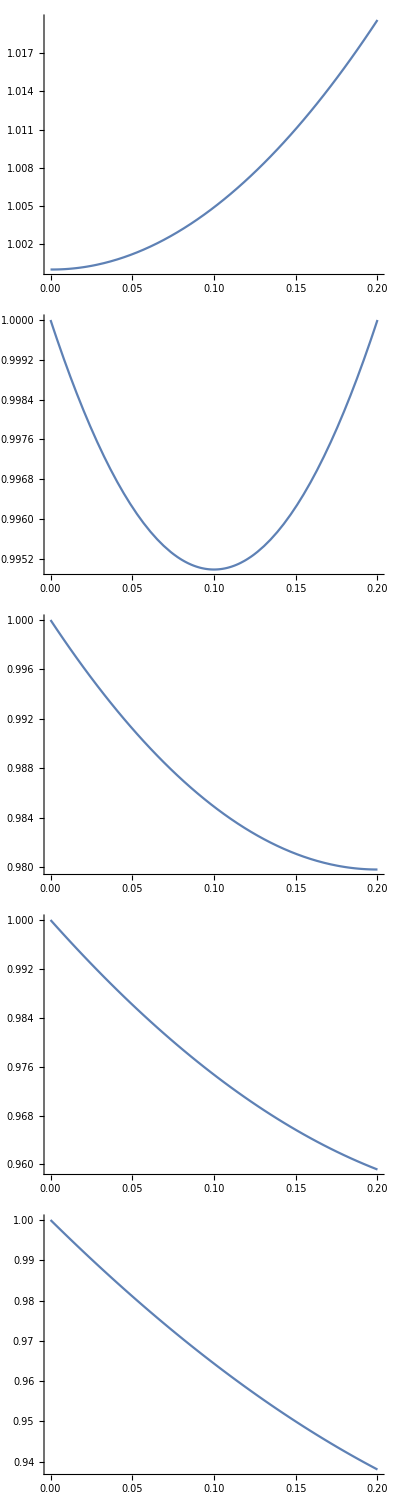

```mathematica
Grid@Table[{Plot[Sqrt[x^2+1-2x i],{x,0,0.2},ImageSize->Medium]},{i,{0.001,0.1,0.2,0.3,0.4}}]
```

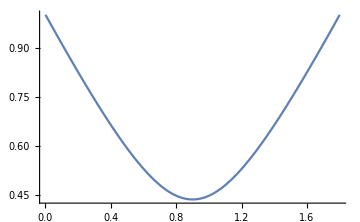

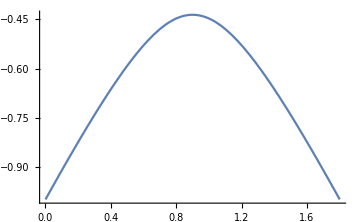

```mathematica
plt1=Plot[Sqrt[x^2+1-2x 0.9],{x,0,1.8},ImageSize->Medium]
plt2=Plot[-Sqrt[x^2+1-2x 0.9],{x,0,1.8},ImageSize->Medium]
```

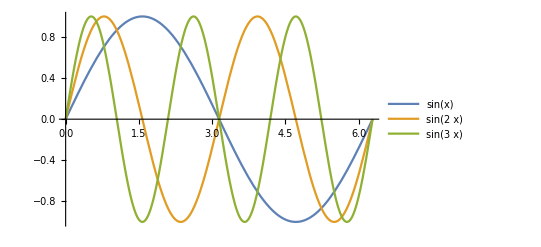

```mathematica
Plot[{Sin[x],Sin[2x],Sin[3x]},{x,0,2Pi},PlotLegends->"Expressions"]
```

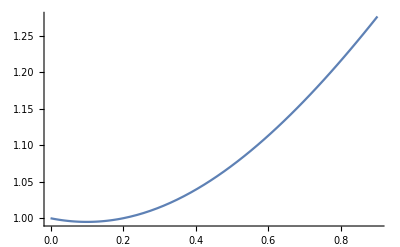
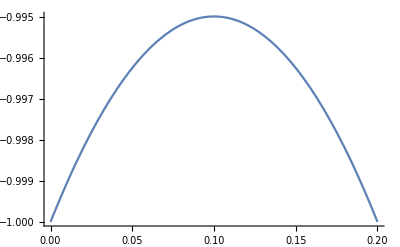
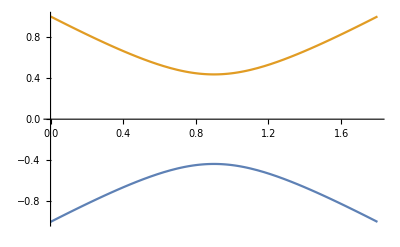

```mathematica
{Plot[√(x^2+1-0.2x),{x,0,0.9}],
Plot[-√(x^2+1-0.2x),{x,0,0.2}],
Plot[{-√(x^2+1-2x 0.9),√(x^2+1-2x 0.9)},{x,0,1.8}]}
```

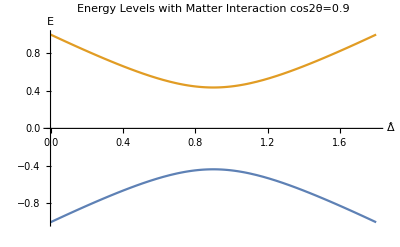

```mathematica
Plot[{-√(x^2+1-2x 0.9),√(x^2+1-2x 0.9)},{x,0,1.8},ImageSize->Full,PlotLabel->"Energy Levels with Matter Interaction\n cos2θ=0.9",AxesLabel->{"Δ̂","E"}]
```

```mathematica
DSolve[y''[x]+I w y'[x]+v^2 y[x]==0,y,x]
```

{{y→Function[{x},ⅇ^(1/2 (-ⅈ w-√(-4 v^2-w^2)) x) C[1]+ⅇ^(1/2 (-ⅈ w+√(-4 v^2-w^2)) x) C[2]]}}